```mathematica
<<MaTeX`
```

```mathematica
T[text_, magn_:1.2]:=MaTeX[text,"Preamble"->{"\\usepackage[T2A]{fontenc}", "\\usepackage{nicefrac}"},Magnification->magn]
```

```mathematica
μ=0.9;S=10;γ=1;
```

```mathematica
S12[x2_]:=-μ x2;
S11[x2_]:=√(1-S12[ x2]^2)+1/S(2/(1-S12[ x2]^2))^((1+γ)/2)
V10[x2_]:=2/μ(√(1-S12[x2]^2)+1/(S(1+γ))(2/(1-S12[x2]^2))^((1+γ)/2))-1/μ(√(1-μ^2)+ArcSin[μ]/μ+2^((3+γ)/2)/(S(1+γ))Hypergeometric2F1[1/2,(1+γ)/2,3/2,μ^2])
```

```mathematica
IntS11=Normal[Integrate[S11[t],{t,-1,1}]];
```

```mathematica
α=0.1;x2=1;C1=1;C2=2;
```

```mathematica
P[x1_]:=1/α μ(1-Abs[x1])-S11[x2]+IntS11
```

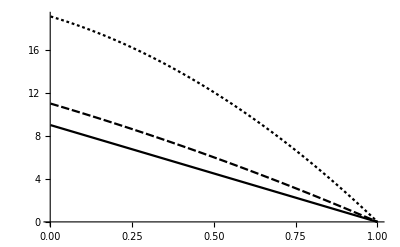

```mathematica
Plot[{P[x]-P[1],P[x]-P[1]+C2(1-x^2),P[x]-P[1]+C1/α(1-x^2)-C1 V10[x2](1-x)},{x,0.001,1},PlotTheme->"Monochrome",PlotLegends->{T["p^\\text{кв}"],T["p\\vert_{\\beta=2}"],T["p\\vert_{\\beta=1}"]},AxesLabel->{T["\\xi_1"],T["\\nicefrac{p}{\\tau_s}",1.5]}]//Quiet
```

```mathematica
Export["F:\\study_dissertation\\Russian-Phd-LaTeX-Dissertation-Template\\images\\ch4\\pressure.pdf",%]
```

F:\study_dissertation\Russian-Phd-LaTeX-Dissertation-Template\images\ch4\pressure.pdf